```mathematica
Clear[ girl, boy ] ;
boy = Import[ "http://imgur.com/mRRhOgo.jpg" ] ;
girl = Import[ "http://imgur.com/Q5ReXSX.jpg" ] ;
gray = RGBColor[0.8353856575309894,0.7865784222185629,0.7943977591036436] ;
(*ColorSeparate[ girl, gray ]*)
```

ColorSeparate::imgcstype: RGBColor[0.835386, 0.786578, 0.794398] is an invalid color space specification.

ColorSeparate[-Graphics-,RGBColor[0.835386,0.786578,0.794398]]

-Graphics-

{RGBColor[0.796541,0.882058,0.908966],RGBColor[0.872855,0.937293,0.952469],RGBColor[0.925359,0.958679,0.967024],RGBColor[0.932523,0.900827,0.911492],RGBColor[0.964756,0.964524,0.961151],RGBColor[0.98015,0.980157,0.980158],RGBColor[0.988344,0.988358,0.98829]}

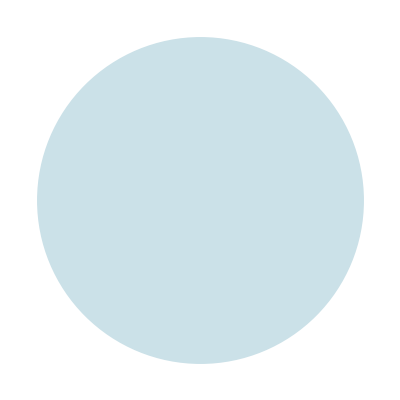
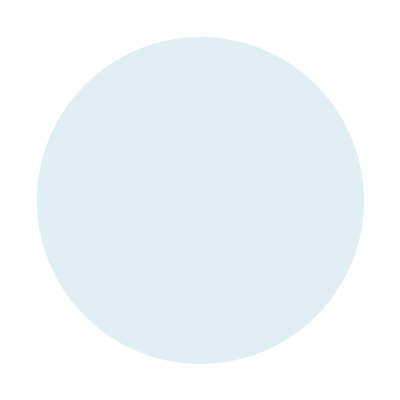
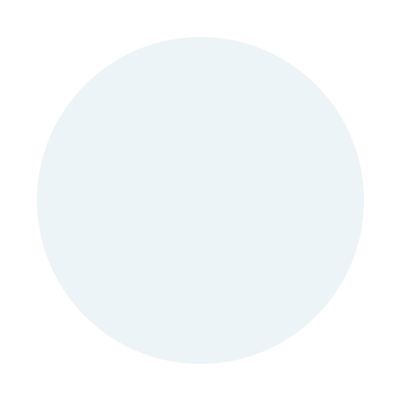
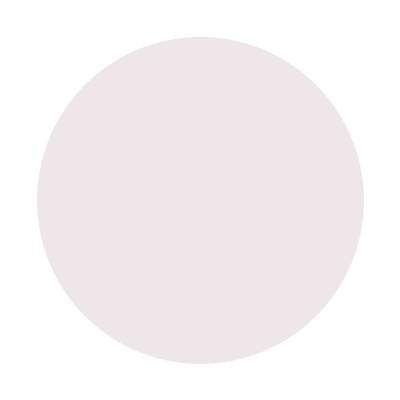
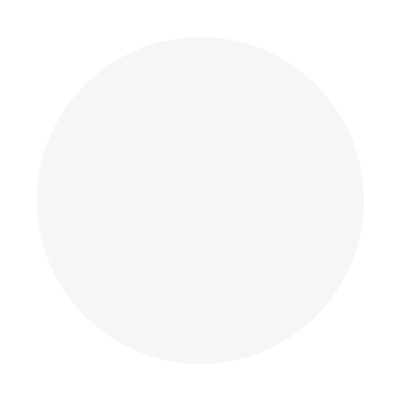
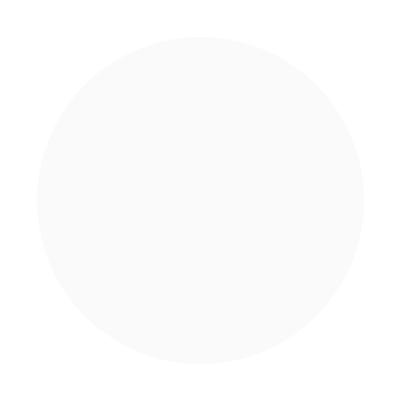
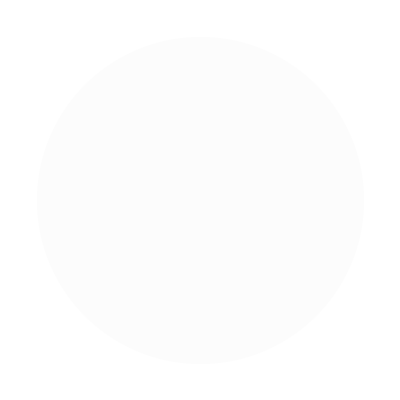

```mathematica
girlSm = ImageResize[ girl, 150 ]
d = DominantColors[CommonestFilter[girlSm,10],7] // Sort
Row[Graphics[{#,Disk[]}]&/@ d]
```

```mathematica
colorExpose[im_,col_,tol_: .005]:=Module[{color=Apply[List,ColorConvert[col,"RGB"]],r=If[ImageColorSpace[im]≠"RGB",ColorConvert[im,"RGB"],im]},SetAlphaChannel[r,Binarize[r,(Norm[#-color]<tol)&]]]

colorExpose[ImageResize[girl, 300],d[[5]], 0.25] // AlphaChannel
```

-Graphics-